# Example : Processing h5 files generated by scqubits

The following uses a sample h5 file provided in the subdirectory ' data'. This file was generated by 
tst = CPB.get_spectrum_vs_paramvals(‘ng’, ng_list, evals_count=4, subtract_ground=False, get_eigenstates=True, filename=’./data/spectrum_vs_ng’),
see the demo.transmon.ipynb jupyter notebook.

```mathematica
SetDirectory[NotebookDirectory[]];
filename="./data/transmon_1.hdf5";
filename="C:\\Users\\drjen\\PycharmProjects\\scqubits\\examples\\sweep-test.h5"
```

C:\Users\drjen\PycharmProjects\scqubits\examples\sweep-test.h5

```mathematica
Import[filename,"StructureGraph"]
```

-Graphics-

First, import the "Attributes" of the h5 file, which reveal the content :

```mathematica
attributes=Import[filename,"Attributes"]/.Association->List//TableForm
```

/→{__type→ParameterSweep,evals_count→20,param_name→flux}
/__objects→{}
/__objects/_hilbertspace→{__type→HilbertSpace}
/__objects/_hilbertspace/__lists→{}
/__objects/_hilbertspace/__lists/interaction_list→{__type→list}
/__objects/_hilbertspace/__lists/interaction_list/__objects→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0→{__type→InteractionTerm,add_hc→0,g_strength→0.1}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0/__objects→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0/__objects/subsys1→{EC→0.2,EJ→20.,__type→Transmon,ncut→40,ng→0.3,truncated_dim→3}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0/__objects/subsys1/__objects→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0/__objects/subsys2→{E_osc→6.,__type→Oscillator,truncated_dim→4}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0/__objects/subsys2/__objects→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0/op1→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/0/op2→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1→{__type→InteractionTerm,add_hc→0,g_strength→0.2}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1/__objects→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1/__objects/subsys1→{EC→0.15,EJ→8.81678,__type→Transmon,ncut→10,ng→0.,truncated_dim→4}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1/__objects/subsys1/__objects→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1/__objects/subsys2→{E_osc→6.,__type→Oscillator,truncated_dim→4}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1/__objects/subsys2/__objects→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1/op1→{}
/__objects/_hilbertspace/__lists/interaction_list/__objects/1/op2→{}
/__objects/_hilbertspace/__lists/subsystem_list→{__type→list}
/__objects/_hilbertspace/__lists/subsystem_list/__objects→{}
/__objects/_hilbertspace/__lists/subsystem_list/__objects/0→{EC→0.2,EJ→20.,__type→Transmon,ncut→40,ng→0.3,truncated_dim→3}
/__objects/_hilbertspace/__lists/subsystem_list/__objects/0/__objects→{}
/__objects/_hilbertspace/__lists/subsystem_list/__objects/1→{EC→0.15,EJ→8.81678,__type→Transmon,ncut→10,ng→0.,truncated_dim→4}
/__objects/_hilbertspace/__lists/subsystem_list/__objects/1/__objects→{}
/__objects/_hilbertspace/__lists/subsystem_list/__objects/2→{E_osc→6.,__type→Oscillator,truncated_dim→4}
/__objects/_hilbertspace/__lists/subsystem_list/__objects/2/__objects→{}
/__objects/_hilbertspace/__objects→{}
/param_vals→{}

The system parameters are stored under "root". The three data sets contain the values of the parameter ' ng', the corresponding eigenenergies, and eigenstates.

It is convenient to handle the different data sets separately and import them one by one. Here, we are interested in making a plot of eigenenergies vs. offset charge, so we import the data sets data_0 and data_1:

```mathematica
ngdata=Import[filename,{"Datasets","/param_vals"}]
```

$Failed

```mathematica
energiesdata=Import[filename,{"Datasets","/SpectrumData/energy_table"}]
```

{{-21.8439,-6.17108,7.93585,20.8401},{-21.8439,-6.17148,7.94339,20.7506},{-21.8439,-6.17259,7.9642,20.5207},{-21.8438,-6.17412,7.99316,20.2339},{-21.8438,-6.17567,8.02296,19.9694},{-21.8438,-6.17684,8.04582,19.7829},{-21.8438,-6.17735,8.05562,19.7067},{-21.8438,-6.17704,8.04967,19.7527},{-21.8438,-6.17601,8.02961,19.9138},{-21.8438,-6.17452,8.00084,20.1631},{-21.8439,-6.17295,7.97093,20.451},{-21.8439,-6.1717,7.9475,20.7034},{-21.8439,-6.1711,7.93633,20.8343},{-21.8439,-6.17131,7.94013,20.7889},{-21.8439,-6.17226,7.95798,20.587},{-21.8439,-6.17372,7.98553,20.3063},{-21.8438,-6.1753,8.01586,20.0299},{-21.8438,-6.1766,8.04114,19.8201},{-21.8438,-6.17729,8.05462,19.7144},{-21.8438,-6.17719,8.05262,19.7298},{-21.8438,-6.17632,8.0357,19.8638},{-21.8438,-6.17491,8.00845,20.0948},{-21.8439,-6.17332,7.97808,20.379},{-21.8439,-6.17196,7.95239,20.6484},{-21.8439,-6.17118,7.93776,20.817},{-21.8439,-6.17118,7.93776,20.817},{-21.8439,-6.17196,7.95239,20.6484},{-21.8439,-6.17332,7.97808,20.379},{-21.8438,-6.17491,8.00845,20.0948},{-21.8438,-6.17632,8.0357,19.8638},{-21.8438,-6.17719,8.05262,19.7298},{-21.8438,-6.17729,8.05462,19.7144},{-21.8438,-6.1766,8.04114,19.8201},{-21.8438,-6.1753,8.01586,20.0299},{-21.8439,-6.17372,7.98553,20.3063},{-21.8439,-6.17226,7.95798,20.587},{-21.8439,-6.17131,7.94013,20.7889},{-21.8439,-6.1711,7.93633,20.8343},{-21.8439,-6.1717,7.9475,20.7034},{-21.8439,-6.17295,7.97093,20.451},{-21.8438,-6.17452,8.00084,20.1631},{-21.8438,-6.17601,8.02961,19.9138},{-21.8438,-6.17704,8.04967,19.7527},{-21.8438,-6.17735,8.05562,19.7067},{-21.8438,-6.17684,8.04582,19.7829},{-21.8438,-6.17567,8.02296,19.9694},{-21.8438,-6.17412,7.99316,20.2339},{-21.8439,-6.17259,7.9642,20.5207},{-21.8439,-6.17148,7.94339,20.7506},{-21.8439,-6.17108,7.93585,20.8401}}

Even though the data is by no means "temporal," the two lists are easily combined into the right form by Mathematica' s TemporalData, and can then be plotted:

```mathematica
plotdata=TemporalData[energiesdata, {ngdata}];
```

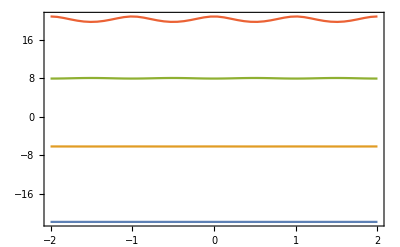

```mathematica
ListPlot[plotdata,Joined->True, Frame->True,Axes->False]
```